# Scattering rate

Want to excite an atom to a Rydberg state near deterministically, given an ensemble of atoms loaded into a dipole trap.

```mathematica
constsdir="..\\constants\\";
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],constsdir}]];
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
<<"rbconsts.m"
```

## single atom in free space

```mathematica
scatter=γ(Int/(2IntS))/(1+(4(2π δ)^2)/γ^2+Int/IntS);
γ =ΓD2;
P = 3.5*^-6;
Int = P/(π*6*^-6*8*^-6);
"Saturation intensity [mW/cm^2]"
IntS =3.05*10^-3*10^4;(*[W/m^2] (ℏ γ (2π (νD2*10^12-2.563*^9+267*^6))^3)/(12π c^2)*);
IntS*10^3*10^-4
```

Saturation intensity [mW/cm^2]

3.05

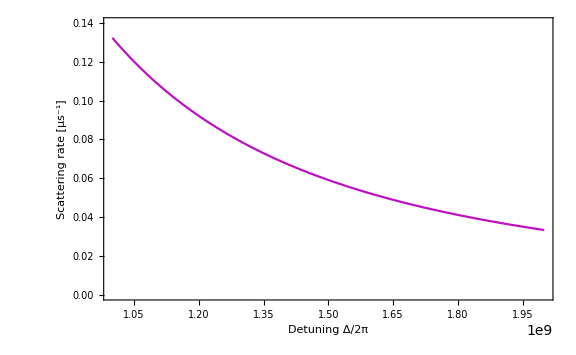

```mathematica
Plot[scatter*1*^-6,{δ,1*^9,2*^9},LabelStyle->Directive[Black,Medium],Axes->Off,Frame->{True,True,False,False},FrameLabel->{"Detuning Δ/2π","Scattering rate [μs^-1]"},PlotStyle->RGBColor[RandomReal[],RandomReal[],RandomReal[]],ImageSize->Large,PlotRange->{0,.14}]
```

So on average, < 0.04 photons are scattered per 1 μs time interval if our light is 2 GHz detuned. For a π pulse to a Rydberg W state with a mean of N atoms is  t_π=π/Ω_N=π/(√N Ω).

```mathematica
"photons scattered during W state pi pulse"
π/(√10 5*^5)*10^6*0.04
```

photons scattered during W state pi pulse

0.0794767